```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
α=1/50;(*GeV/fm*)
R=10;(*fm*)
mπ=13957/100000;(*GeV*)
```

```mathematica
precision=8;
multiplicity=1000;
data={};
multdata={};
For[i=0,i<10000,i++,
(*xyzPts=RandomVariate[MultinormalDistribution[{0,0,0},DiagonalMatrix[{R^2/2,R^2/2,R^2/2}]],multiplicity];
KPts=α xyzPts;
EKPts=ArrayReshape[√(mπ^2+KPts[[;;,1]]^2+KPts[[;;,2]]^2+KPts[[;;,3]]^2),{multiplicity,1}];*)
zPts=ArrayReshape[RandomVariate[NormalDistribution[0,R/(√2)],multiplicity],{multiplicity,1}];
KzPts=α zPts;
KxPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
KyPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
EKPts=√(mπ^2+KzPts^2);
eventIndex=ArrayReshape[Table[i,{j,multiplicity}],{multiplicity,1}];
tPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
xPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
yPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
particleIndices=ArrayReshape[Range[multiplicity],{multiplicity,1}];
(*Print[eventIndex,particleIndices,EKPts,KPts,tPts,xyzPts];
Print[Join[eventIndex,particleIndices,EKPts,KPts,tPts,xyzPts,2]//Dimensions];*)
(*AppendTo[data,Flatten[Join[eventIndex,particleIndices,SetPrecision[EKPts,precision],SetPrecision[KPts,precision],SetPrecision[tPts,precision],SetPrecision[xyzPts,precision],2],{1}]]*)
AppendTo[data,Flatten[Join[eventIndex,particleIndices,SetPrecision[EKPts,precision],SetPrecision[KxPts,precision],SetPrecision[KyPts,precision],SetPrecision[KzPts,precision],SetPrecision[tPts,precision],SetPrecision[xPts,precision],SetPrecision[yPts,precision],SetPrecision[zPts,precision],2],{1}]];
AppendTo[multdata,{i,multiplicity,multiplicity}]
]
data=Flatten[data,1];
data//Dimensions
Export[NotebookDirectory[]~StringJoin~"toyOSCAR.dat",Append[data,""]]
Export[NotebookDirectory[]~StringJoin~"toyOSCAR_mult.dat",Append[multdata,""]]
```

{10000000,10}

/home/blixen/plumberg/HBT_event_generator/HBT_event_generator_w_errors/checks/toyOSCAR.dat

/home/blixen/plumberg/HBT_event_generator/HBT_event_generator_w_errors/checks/toyOSCAR_mult.dat

```mathematica
(*numerator*)
num=Abs[FourierTransform[Exp[-(x^2+y^2+z^2)/R^2]DiracDelta[Kx-α x]DiracDelta[Ky-α y]DiracDelta[Kz-α z],{x,y,z},{qx,qy,qz},Assumptions->α>0,FourierParameters->{1,1}]]^2//ComplexExpand
(*denominator*)
den=Integrate[Exp[-(x^2+y^2+z^2)/R^2]DiracDelta[Kx+qx/2-α x]DiracDelta[Ky+qy/2-α y]DiracDelta[Kz+qz/2-α z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->α>0&&Kx>0&&Ky>0&&Kz>0&&qx>0&&qy>0&&qz>0]Integrate[Exp[-(x^2+y^2+z^2)/R^2]DiracDelta[Kx-qx/2-α x]DiracDelta[Ky-qy/2-α y]DiracDelta[Kz-qz/2-α z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->α>0&&Kx>0&&Ky>0&&Kz>0&&qx>0&&qy>0&&qz>0]//FullSimplify
(*denominator*)
correlator=num/den//FullSimplify
```

15625000000 ⅇ^(-50 Kx^2-50 Ky^2-50 Kz^2)

15625000000 ⅇ^(-25/2 (4 Kx^2+4 Ky^2+4 Kz^2+qx^2+qy^2+qz^2))

ⅇ^(25/2 (qx^2+qy^2+qz^2))

```mathematica
(1./(2 α^2 R^2))
```

12.5

```mathematica
precision=8;
multiplicity=1000000;
data={};
multdata={};
For[i=0,i<10,i++,
xyzPts=RandomVariate[MultinormalDistribution[{0,0,0},DiagonalMatrix[{R^2/2,R^2/2,R^2/2}]],multiplicity];
KPts=α xyzPts;
EKPts=ArrayReshape[√(mπ^2+KPts[[;;,1]]^2+KPts[[;;,2]]^2+KPts[[;;,3]]^2),{multiplicity,1}];
eventIndex=ArrayReshape[Table[i,{j,multiplicity}],{multiplicity,1}];
tPts=ArrayReshape[Table[0,{j,multiplicity}],{multiplicity,1}];
particleIndices=ArrayReshape[Range[multiplicity],{multiplicity,1}];
AppendTo[data,Flatten[Join[eventIndex,particleIndices,SetPrecision[EKPts,precision],SetPrecision[KPts,precision],SetPrecision[tPts,precision],SetPrecision[xyzPts,precision],2],{1}]]
AppendTo[multdata,{i,multiplicity,multiplicity}]
]
data=Flatten[data,1];
data//Dimensions
Export[NotebookDirectory[]~StringJoin~"toyOSCAR3D.dat",Append[data,""]]
Export[NotebookDirectory[]~StringJoin~"toyOSCAR3D_mult.dat",Append[multdata,""]]
```

{10000000,10}

/home/blixen/plumberg/HBT_event_generator/HBT_event_generator_w_errors/checks/toyOSCAR3D.dat

/home/blixen/plumberg/HBT_event_generator/HBT_event_generator_w_errors/checks/toyOSCAR3D_mult.dat

```mathematica
(0.03-(-0.03))/0.005
```

12.

```mathematica
α=1/50;(*GeV/fm*)
R=10;(*fm*)
```

```mathematica
(*numerator*)
num=Abs[FourierTransform[Exp[-z^2/R^2]DiracDelta[Kz-α z],z,qz,Assumptions->α>0,FourierParameters->{1,1}]]^2//ComplexExpand
(*denominator*)
den=Integrate[Exp[-z^2/R^2]DiracDelta[Kz+qz/2-α z],{z,-∞,∞},Assumptions->α>0&&Kz>0&&qz>0]Integrate[Exp[-z^2/R^2]DiracDelta[Kz-qz/2-α z],{z,-∞,∞},Assumptions->α>0&&Kz>0&&qz>0]//FullSimplify
(*denominator*)
correlator=num/den//FullSimplify
```

(ⅇ^(-(2 Kz^2)/(R^2 α^2)))/α^2

(ⅇ^(-(4 Kz^2+qz^2)/(2 R^2 α^2)))/α^2

ⅇ^(qz^2/(2 R^2 α^2))

```mathematica
Clear[R,α]
Integrate[1/(√π R)Exp[-z^2/R^2]DiracDelta[Kz-α z],{z,-∞,∞},{Kz,-∞,∞},Assumptions->R>0]
```

1

```mathematica
25/π//N
```

7.95775

```mathematica
Δpz=0.005
NperEvent=10000
NperEvent(NperEvent-1)
```

0.005

10000

99990000

```mathematica
α=1/50;(*GeV/fm*)
R=10;(*fm*)
Integrate[10^3/(√π R α)Exp[-K0^2/(α^2 R^2)],{K0,-0.0025,0.0025},Assumptions->R>0&&α>0]
2%(%-1)
```

14.104

369.638

```mathematica
Integrate[(1/ϵ)^2 UnitBox[pi/ϵ]UnitBox[pj/ϵ]/.ϵ->1,{pi,-∞,∞},{pj,-∞,∞}]
Integrate[(1/(2ϵ))UnitBox[(pi-pj)/(2ϵ)](1/ϵ)UnitBox[(pi+pj)/(2ϵ)]/.ϵ->1,{pi,-∞,∞},{pj,-∞,∞}]
```

1

1

```mathematica
FourierTransform[Exp[-(z^2)/R^2]DiracDelta[Kz-α z],{z},{0},Assumptions->α>0,FourierParameters->{1,1}]
```

(ⅇ^(-Kz^2/(R^2 α^2)))/α

```mathematica
n=2500;
α=1/50;(*GeV/fm*)
R=10;(*fm*)
bw=0.005;
data=RandomVariate[MultinormalDistribution[{0,0,0},DiagonalMatrix[{(α^2 R^2)/2,(α^2 R^2)/2,(α^2 R^2)/2}]],n];
nChosenPairs=Count[Subsets[data,{2}],x_/;(Abs[#[[1,1]]-#[[2,1]]]≤bw&&Abs[#[[1,2]]-#[[2,2]]]≤bw&&Abs[#[[1,3]]-#[[2,3]]]≤bw)&[x]];
(2nChosenPairs)/(n(n-1)(1bw)^3)//N
```

61.4646

```mathematica
(*numerator*)
num=Abs[FourierTransform[Exp[-(x^2+y^2+z^2)/(R^2)],{x,y,z},{qx,qy,qz},Assumptions->R>0,FourierParameters->{1,1}]]^2//ComplexExpand
(*denominator*)
den=Integrate[Exp[-(x^2+y^2+z^2)/(R^2)],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->R>0]Integrate[Exp[-(x^2+y^2+z^2)/(R^2)],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->R>0]//FullSimplify
(*denominator*)
correlator=num/den//FullSimplify
```

(π^3 R^6)/(√(ⅇ^((qx^2+qy^2+qz^2) R^2)))

π^3 R^6

1/(√(ⅇ^((qx^2+qy^2+qz^2) R^2)))

```mathematica
Integrate[Exp[-Abs[(x Rx)^2+(y Ry)^2+(z Rz)^2]^(α/2)],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->0<α≤2 && Rx>0&& Ry>0&& Rz>0]
```

(4 π Gamma[(3+α)/α])/(3 Rx Ry Rz)

```mathematica
Integrate[Exp[-((x Rx)^2+(y Ry)^2+(z Rz)^2+2x y Rxy+2y z Ryz+2x z Rxz)],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->0<α≤2 && Rx>0&& Ry>0&& Rz>0&& Rxy>0&& Ryz>0&& Rxz>0]
```

ConditionalExpression[π/(√(-Ryz^2+Ry^2 Rz^2) √((Rxz^2 Ry^2-2 Rxy Rxz Ryz+Rx^2 Ryz^2+Rxy^2 Rz^2-Rx^2 Ry^2 Rz^2)/(π Ryz^2-π Ry^2 Rz^2))),(Ryz-Ry Rz) (Rxz^2 Ry^2-2 Rxy Rxz Ryz+Rxy^2 Rz^2+Rx^2 (Ryz-Ry Rz) (Ryz+Ry Rz))>0]

```mathematica
Rxz^2 Ry^2-2 Rxy Rxz Ryz+Rx^2 Ryz^2+Rxy^2 Rz^2-Rx^2 Ry^2 Rz^2==-Det[{{Rx^2,Rxy,Rxz},{Rxy,Ry^2,Ryz},{Rxz,Ryz,Rz^2}}]//Expand
```

True

```mathematica
Refine[Integrate[Exp[-((x Rx)^2+(y Ry)^2+2x y Rxy)],{x,-∞,∞},{y,-∞,∞},Assumptions->0<α≤2 && Rx>0&& Ry>0&& Rx Ry≥Rxy>0],0<α≤2 && Rx>0&& Ry>0&& Rx Ry≥Rxy>0]
Det[{{Rx^2,Rxy},{Rxy,Ry^2}}]
```

π/(√(-Rxy^2+Rx^2 Ry^2))

-Rxy^2+Rx^2 Ry^2

```mathematica
(*numerator*)
num=Abs[FourierTransform[Exp[-z^2/R^2]Exp[-Kz^2/σK^2],z,qz,Assumptions->R>0,FourierParameters->{1,1}]]^2//ComplexExpand
(*denominator*)
den=Integrate[Exp[-z^2/R^2]Exp[-(Kz+qz/2)^2/σK^2],{z,-∞,∞},Assumptions->R>0]Integrate[Exp[-z^2/R^2]Exp[-(Kz-qz/2)^2/σK^2],{z,-∞,∞},Assumptions->R>0]//FullSimplify
(*denominator*)
correlator=num/den//FullSimplify
```

ⅇ^(-1/2 qz^2 R^2-(2 Kz^2)/σK^2) π R^2

ⅇ^(-(4 Kz^2+qz^2)/(2 σK^2)) π R^2

ⅇ^(-(qz^2 (-1+R^2 σK^2))/(2 σK^2))

```mathematica
TransformedDistribution[KT Cos[Φ],{KT\[Distributed]ExponentialDistribution[1],Φ\[Distributed]UniformDistribution[{0,2π}]}]
```

TransformedDistribution[x1 Cos[x2],{x1\[Distributed]ExponentialDistribution[1],x2\[Distributed]UniformDistribution[{0,2 π}]}]

```mathematica
TransformedDistribution[u^2+v^2,{u\[Distributed]NormalDistribution[0,σ],v\[Distributed]NormalDistribution[0,σ]}]
```

ExponentialDistribution[1/(2 σ^2)]

```mathematica
TransformedDistribution[√x,x\[Distributed]ExponentialDistribution[1/(2 σ^2)],Assumptions->σ>0]
```

WeibullDistribution[2,√2 σ]

```mathematica
S[x_,y_,z_,px_,py_,pz_]:=Exp[-((px^2+py^2+pz^2)/T^2)]Exp[-((x^2+y^2+z^2)/R^2)];
num=FourierTransform[S[x,y,z,Kx,Ky,Kz],{x,y,z},{qx,qy,qz},Assumptions->Kx>0&&Ky>0&&T>0&&w>0&&R>0,FourierParameters->{1,1}]^2//FullSimplify
den=Integrate[S[x,y,z,Kx+qx/2,Ky+qy/2,Kz+qz/2],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->Kx>0&&Ky>0&&qx>0&&qy>0&&T>0&&w>0&&R>0]Integrate[S[x,y,z,Kx-qx/2,Ky-qy/2,Kz-qz/2],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->Kx>0&&Ky>0&&qx>0&&qy>0&&T>0&&w>0&&R>0]//FullSimplify
denSmooth=Integrate[S[x,y,z,Kx,Ky,Kz],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->Kx>0&&Ky>0&&qx>0&&qy>0&&T>0&&w>0&&R>0]^2//FullSimplify
FullSimplify[num/den,R>0&&T>0&&w>0]
FullSimplify[num/denSmooth,R>0&&T>0&&w>0]
```

ⅇ^(-1/2 (qx^2+qy^2+qz^2) R^2-(2 (Kx^2+Ky^2+Kz^2))/T^2) π^3 R^6

ⅇ^(-(4 Kx^2+4 Ky^2+4 Kz^2+qx^2+qy^2+qz^2)/(2 T^2)) π^3 R^6

ⅇ^(-(2 (Kx^2+Ky^2+Kz^2))/T^2) π^3 R^6

ⅇ^(-((qx^2+qy^2+qz^2) (-1+R^2 T^2))/(2 T^2))

ⅇ^(-1/2 (qx^2+qy^2+qz^2) R^2)

```mathematica
%395/.{R->3/0.19733,T->0.12}//FullSimplify
%396/.{R->3/0.19733,T->0.12}//FullSimplify
```

ⅇ^(-80.8428 (qx^2+qy^2+qz^2))

ⅇ^(-115.565 (qx^2+qy^2+qz^2))

```mathematica
115.56498892300593 0.19733^2
```

4.5

```mathematica
num=Refine[num//.{Kx->KT Cos[ΦK],Ky->KT Sin[ΦK],qx->qo Cos[ΦK]-qs Sin[ΦK],qy->qo Sin[ΦK]+qs Cos[ΦK]}//Factor//Simplify,KT>0]
```

4 ⅇ^(-(qo^2+qs^2) R^2-(2 KT^2)/T^2) π^2 R^4

```mathematica
den=Refine[den//.{Kx->KT Cos[ΦK],Ky->KT Sin[ΦK],qx->qo Cos[ΦK]-qs Sin[ΦK],qy->qo Sin[ΦK]+qs Cos[ΦK]}//Factor//Simplify,KT>0]
```

4 ⅇ^(-(4 KT^2+qo^2+qs^2)/(2 T^2)) π^2 R^4

```mathematica
Refine[den/.{qo->0,qs->0},KT>0]
```

4 ⅇ^(-(2 KT^2)/T^2) π^2 R^4

```mathematica
Integrate[%274/.{qo->0,qs->0},{KT,0,1/5}]
```

2 (1-ⅇ^(-2/5/T)) π^2 R^4 T

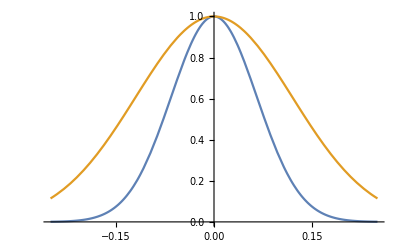

```mathematica
numNorm=NIntegrate[num/.{qo->0,qs->0,R->(3/√2)/0.19733,T->0.12},{KT,0,0.2}];
denNorm=NIntegrate[den/.{qo->0,qs->0,R->(3/√2)/0.19733,T->0.12},{KT,0,0.2}];
Plot[{NIntegrate[num/numNorm/.{qo->0,qs->0,R->(3/√2)/0.19733,T->0.12},{KT,0,0.2}],NIntegrate[den/denNorm/.{qo->0,qs->0,R->(3/√2)/0.19733,T->0.12},{KT,0,0.2}]},{qs,-0.25,0.25}]
```